# JAGROS, d.o.o.

```mathematica
Labeled[Import["C:\Users\HP\Desktop\Računalniška orodja v matematiki\Logotip podjetja.png"],
	       Text["Slika 1: Logotip podjetja"]]
```

-Graphics-Slika 1: Logotip podjetja

```mathematica
Hyperlink["https://www.trgovinejager.com/"]
```

https://www.trgovinejager.com/

## OSNOVNI PODATKI

- JAGROS, d.o.o. je zasebno slovensko družinsko podjetje
- glavna dejavnost podjetja je maloprodaja živilskega in neživilskega blaga
- SEDEŽ PODJETJA: Prvomajska ulica 29, 3250 Rogaška Slatina
- podjetje sta ustanovila Franc in Marija Jager, danes podjetje vodita Aleš in Boštjan Jager

```mathematica
Labeled[Framed[PieChart3D[{56,20,20,4},
	                                             ChartLabels->{"56 %","20 %","20 %","4 %"},
	                                             ChartLegends->{"JAGROS, d.o.o.","Aleš Jager","Boštjan Jager","Marija Jager"}]],
                                Text["Diagram 1: Delež ustanoviteljev"]]
```

-Graphics3D-Diagram 1: Delež ustanoviteljev

```mathematica
Labeled[Import["C:\Users\HP\Desktop\Računalniška orodja v matematiki\Družina Jager.jpg"],
	       Text["Slika 2: Družina Jager"]]
```

-Graphics-Slika 2: Družina Jager

- podjetje je med stranskami prepoznavno pod imenom Trgovine Jager, posluje v 41 maloprodajnih poslovnih enotah ter v centralnem skladišču Mestinje

```mathematica
mesta={{"BistricaObDravi","Podravska"},{"Velenje","Savinjska"},{"SelnicaObDravi","Podravska"},{"Rogatec","Savinjska"},{"Radenci","Pomurska"},{"Pragersko","Podravska"},{"Prebold","Savinjska"},{"Odranci","Pomurska"},{"Celje","Savinjska"},{"Mozirje","Savinjska"},{"Ljutomer","Pomurska"},{"SpodnjiDuplek","Podravska"},{"Maribor","Podravska"}};
```

```mathematica
obcine={"Gorišnica","Ptuj","Braslovče","Turnišče","TrnovskaVas","Starše","Šentilj","Vransko","Poljčane","Podčetrtek","Kidričevo","Majšperk","Krško","Kozje","ŠmarjePriJelšah","BistricaObSotli"};
```

```mathematica
mestaKjerSoPoslovalnice=Map[Apply[Entity["City",{##,"Slovenia"}]&,#]&,mesta];
```

```mathematica
obcineKjerSoPoslovalnice=Map[Function[enota,Entity["AdministrativeDivision",{enota,"Slovenia"}]],obcine];
```

```mathematica
poslovalnice=Join[mestaKjerSoPoslovalnice,obcineKjerSoPoslovalnice];
```

```mathematica
Labeled[GeoListPlot[poslovalnice,GeoRange->Entity["Country","Slovenia"]],Text["Zemljevid 1: Poslovalnice Trgovin Jager"]]
```

-Graphics-Zemljevid 1: Poslovalnice Trgovin Jager

```mathematica
mesta={{"BistricaObDravi","Podravska",2792},{"Velenje","Savinjska",25132},{"SelnicaObDravi","Podravska",1084},{"Rogatec","Savinjska",2998},{"Radenci","Pomurska",2125},{"Pragersko","Podravska",2074},{"Prebold","Savinjska",3281},{"Odranci","Pomurska",1342},{"Celje","Savinjska",49593},{"Mozirje","Savinjska",3342},{"Ljutomer","Pomurska",3375},{"SpodnjiDuplek","Podravska",3264},{"Maribor","Podravska",111374}};
```

```mathematica
tabelaRegijPoslovalnic=Dataset[Map[<|"Mesto"->#[[1]],"Regija"->#[[2]],"Prebivalci"->#[[3]]|>&,mesta]]
```

```mathematica
povprecjePrihodkovODProdajeNaPoslovalnico2022=Round[215400000/41];
```

```mathematica
pridodkiOdProdajePoslovalnicVTabeli=povprecjePrihodkovODProdajeNaPoslovalnico2022*13;
```

```mathematica
skupnoSteviloPrebivalcevVTabeli=Total[mesta[[All,3]]];
```

```mathematica
prihodkiOdProdajeGledeSteviloPrebivalcevMesta=Round[povprecjePrihodkovODProdajeNaPoslovalnico2022*mesta[[All,3]]/skupnoSteviloPrebivalcevVTabeli];
```

```mathematica
tabelaRegijPoslovalnic=Dataset[Prepend[MapThread[Append[#1,#2]&,{mesta,prihodkiOdProdajeGledeSteviloPrebivalcevMesta}],{"Mesto","Regija","Prebivalci","Prihodki od prodaje (eur)"}]]
```

JoinAcross::ntable: Dataset at position 2 does not contain a valid list of associations.

JoinAcross::invlc: The argument Dataset[«13»] is not a list of Associations.

General::interr2: An unknown internal error occurred. Consult Internal`$LastInternalFailure for potential information.

## POSLOVANJE

- podjetje uspešno posluje že od samega začetka, zavezano je k spoštovanju poslovnosti in se prednostno oskrbuje v lokalnem okolju

- PRIHODKI OD PRODAJE: vsi skupni fakturirani zneski, ki jih opazovana enota zaračuna v nekem odbdobju
- POSLOVNI IZID POSLOVANJA: razlika med prihodki od prodaje in stroški poslovanja podjetja v nekem obdobju
- ČISTI DOBIČEK: dobiček, ki ga podjetje ustvari po odštevanju vseh stroškov od prihodkov

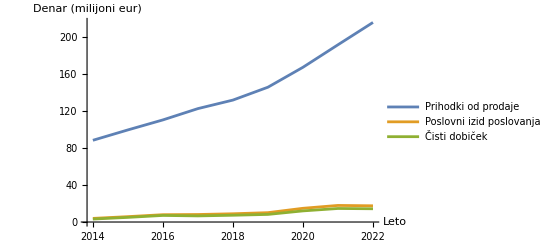
-Graphics-Graf 1: Poslovanje podjetja

```mathematica
Labeled[Framed[ListLinePlot[{{88.2,99.4,110.2,122.4,131.6,145.5,167.0,191.3,215.4},
                                                         {3.9,5.8,7.9,8.1,8.9,10.1,14.8,17.9,17.5},
                                                         {3.2,5.0,7.1,6.6,7.3,8.2,12.0,14.6,14.3}},
                                                             PlotLegends->{"Prihodki od prodaje","Poslovni izid poslovanja","Čisti dobiček"},
                                                             AxesLabel->{"Leto","Denar (milijoni eur)"},
                                                             DataRange->{2014,2022}]],
                Text["Graf 1: Poslovanje podjetja"]]
```

## Povprečen čisti dobiček, poslovni izid in prihodki prodaje med leti 2014-2022

```mathematica
cistiDobicek={3200000,5000000,7100000,6600000,7300000,8200000,12000000,14600000,14300000};
```

```mathematica
poslovniIzid={3900000,5800000,7900000,8100000,8900000,10100000,14800000,17900000,17500000};
```

```mathematica
prihodkiProdaje={88200000,99400000,110200000,122400000,131600000,145500000,167000000,191300000,215400000};
```

```mathematica
tabelePoslovanjePodjetja ={cistiDobicek,poslovniIzid,prihodkiProdaje};
```

```mathematica
skupneVsotePoslovanje=Map[Total,tabelePoslovanjePodjetja];
```

```mathematica
povprecnoPoslovanje=Round[skupneVsotePoslovanje/9]
```

{8700000,10544444,141222222}

- BILANČNA VSOTA: skupna vrednost vseh sredtev, ki jih ima podjetje ter vse obveznosti, ki jih ima do drugih subjektov
- KAPITAL: trajen vir financiranja, ki ga v podjetje vložijo lastniki ali pa je nastal z uspešnim poslovanjem podjetja
- VLAGANJE V OSNOVNA SREDSTVA: naložbe, v katere podjetje vlaga (dolgoročne naložbe)

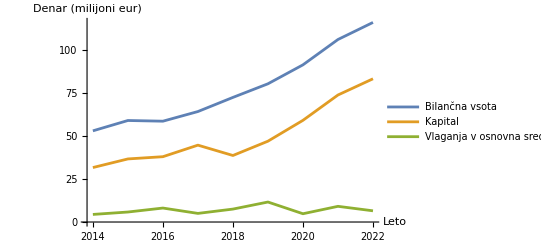
-Graphics-Graf 2: Poslovanje podjetja

```mathematica
Labeled[Framed[ListLinePlot[{{52.9,58.9,58.5,64.1,72.3,80.2,91.2,105.9,115.8},
                                                         {31.6,36.6,37.9,44.6,38.6,46.9,59.0,73.7,83.1},
                                                         {4.4,5.8,8.1,5.0,7.5,11.6,4.8,9.1,6.5}},
                                                             PlotLegends->{"Bilančna vsota","Kapital","Vlaganja v osnovna sredstva"},
                                                             AxesLabel->{"Leto","Denar (milijoni eur)"},
                                                             DataRange->{2014,2022}]],
               Text["Graf 2: Poslovanje podjetja"]]
```

PRIHODKI OD PRODAJE PO SEGMENTIH:

```mathematica
Row[{Labeled[Framed[PieChart[{57,37,5,1},
	                                               ChartLegends->{"Živila (57 %)","Tehnika (37 %)","Tekstil (5 %)","Gostinstvo (1 %)"}]],
                                       Text["Prihodki od prodaje 2018"]],
      Labeled[Framed[PieChart[{57,37,5,1},
	                                              ChartLegends->{"Živila (57 %)","Tehnika (37 %)","Tekstil (5 %)","Gostinstvo (1 %)"}]],
                                      Text["Prihodki od prodaje 2019"]],
      Labeled[Framed[PieChart[{58,38,3,1},
	                                              ChartLegends->{"Živila (58 %)","Tehnika (38 %)","Tekstil (3 %)","Gostinstvo (1 %)"}]],  
                                      Text["Prihodki od prodaje 2020"]],
      Labeled[Framed[PieChart[{53,41,4,1,1},
	                                              ChartLegends->{"Živila (53 %)","Tehnika (41 %)","Tekstil (4 %)","Gostinstvo (1 %)","Ostale storitve (1%)"}]], 
                                      Text["Prihodki od prodaje 2021"]],
      Labeled[Framed[PieChart[{52,42,4,1,1},
	                                              ChartLegends->{"Živila (52 %)","Tehnika (42 %)","Tekstil (4 %)","Gostinstvo (1 %)","Ostale storitve (1%)"}]],
                                      Text["Prihodki od prodaje 2022"]]}]
```

-Graphics-Prihodki od prodaje 2018-Graphics-Prihodki od prodaje 2019-Graphics-Prihodki od prodaje 2020-Graphics-Prihodki od prodaje 2021-Graphics-Prihodki od prodaje 2022

## POVPREČJE PRINOSA PRIHODKOV PO SEGMENTIH PRODAJE MED LETI 2018-2022

```mathematica
prihodki2018={57,37,5,1,0};
```

```mathematica
prihodki2019={57,37,5,1,0};
```

```mathematica
prihodki2020={58,38,3,1,0};
```

```mathematica
prihodki2021={53,41,4,1,1};
```

```mathematica
prihodki2022={52,42,4,1,1};
```

```mathematica
dolzinaTabel=Length[prihodki2018];
```

```mathematica
poprecjePrihodkovProdaje=Table[0,{dolzinaTabel}];
```

```mathematica
For[i=1,i<=dolzinaTabel,i++,
          poprecjePrihodkovProdaje[[i]]=Round[(prihodki2018[[i]]+prihodki2019[[i]]+prihodki2020[[i]]+prihodki2021[[i]]+prihodki2022[[i]])/dolzinaTabel]]
```

```mathematica
poprecjePrihodkovProdaje
```

{55,39,4,1,0}

## ZAPOSLENI

- podjetje se trudi zaposlenim nuditi prijazno, varno in stabilno delovno okolje
- spodbujajo osebnostno in strokovno rast vsakega posameznika

```mathematica
leta[leto_]:="Leto: "<>ToString[leto]
```

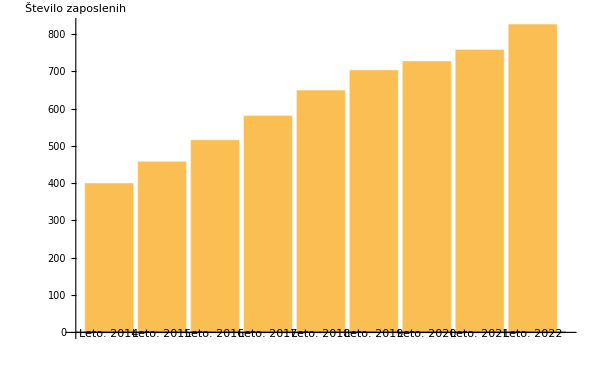
-Graphics-Diagram 2: Število zaposlenih skozi leta

```mathematica
Labeled[BarChart[{399,457,515,580,648,702,726,757,825},
                                   ChartLabels->Table[leta[leto],
                                                                         {leto,2014,2022}],
                                   ImageSize->{600,400},
                                   AxesLabel->{None,"Število zaposlenih"}],
	       Text["Diagram 2: Število zaposlenih skozi leta"]]
```

```mathematica
zaposleneŽenske={{490},{509},{504},{542},{586}}
```

{{490},{509},{504},{542},{586}}

```mathematica
zaposleniMoški={{231},{262},{260},{278},{303}}
```

{{231},{262},{260},{278},{303}}

```mathematica
skupajZaposleni=MapThread[Plus,{zaposleneŽenske,zaposleniMoški}]
```

{{721},{771},{764},{820},{889}}

```mathematica
Labeled[Framed[TableForm[{zaposleneŽenske,
                                                   Round[100*zaposleneŽenske/skupajZaposleni],
                                                   zaposleniMoški,
                                                    Round[100*zaposleniMoški/skupajZaposleni]}, 
                                                      TableHeadings->{{"Zaposlene ženske","Odstotek žensk (%)","Zaposleni moški","Odstotek moških (%)"}, 
                                                                                        {"2018","2019","2020","2021","2022"}}]],      
                Text["Tabela 1: Število in odstotek zaposlenih glede na spol"]]
```

| 2018 | 2019 | 2020 | 2021 | 2022
Zaposlene ženske | 490 | 509 | 504 | 542 | 586
Odstotek žensk (%) | 68 | 66 | 66 | 66 | 66
Zaposleni moški | 231 | 262 | 260 | 278 | 303
Odstotek moških (%) | 32 | 34 | 34 | 34 | 34Tabela 1: Število in odstotek zaposlenih glede na spol

```mathematica
Labeled[Import["C:\\Users\\HP\\Desktop\\Računalniška orodja v matematiki\\Vrsta zaposlitve.xlsx","Dataset","HeaderLines"->1]//First,
                Text["Tabela 2: Število zaposlitev za določen / nedoločen čas in število na novo sklenjenih / prekinjenih delovnih razmerij"]]
```

Tabela 2: Število zaposlitev za določen / nedoločen čas in število na novo sklenjenih / prekinjenih delovnih razmerij

```mathematica
Labeled[Import["C:\\Users\\HP\\Desktop\\Računalniška orodja v matematiki\\Povprečna plača.xlsx","Dataset","HeaderLines"->1]//First//
                              Query[All,
                                         <|#,"Povprečna mesečna plača (€)"->#["Stroški plač (€)"]/12/#["Število zaposlenih"]|>&],
                Text["Tabela 3: Stroški plač in povprečna mesečna plača"]]
```

Tabela 3: Stroški plač in povprečna mesečna plača

## RAČUNOVODSKI IZKAZ

- DOLGOROČNA SREDSTVA:
	- opredmetena osnovna sredstva,
	- dolgoročne finančne naložbe,
	- odložene terjatve za davek, ...
- KRATKOROČNA SREDSTVA:
	- sredstva za prodajajo,
	- zaloge,
	- kratkoročne finančne naložbe, ...
- KRATKOROČNE AKTIVNE ČASOVNE RAZMEJITVE:

```mathematica
podatkiZaRačunovodskiIzkaz=Import["C:\\Users\\HP\\Desktop\\Računalniška orodja v matematiki\\Datoteke za projektno nalogo\\Računovoski izkaz.xlsx","Dataset","HeaderLines"->1]//First
```

```mathematica
podatkiZaRačunovodskiIzkaz//Query[All,<|#,"Skupaj (€)"->#["Dolgoročna sredstva (€)"]+#["Kratkoročna sredstva (€)"]+#["Kratkoročne časovne razmejitve (€)"]|>&]
```

```mathematica
Export["/mnt/data/obdelani_podatki.xlsx",podatkiZNovimStolpcem]
```

/mnt/data/obdelani_podatki.xlsx

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[Failure[Prepend,<|MessageTemplate:>Prepend::invdt,MessageParameters→{Vsote}|>],Vsote].